```mathematica
Clear[x];
```

```mathematica
Clear[y];
```

```mathematica
f1[t_,x_,y_]:=t*x- Sin[y]
f2[t_,x_,y_]:=Cos[t]*x-y Sin[x];
```

```mathematica
x[0]=.2
```

0.2

0.2

0.01

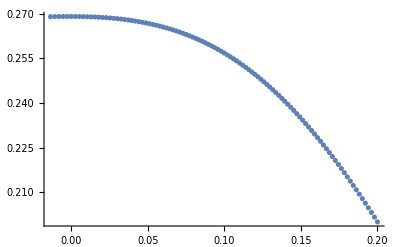

```mathematica
y[0]=.2
h=.01
Do[{x[n]=x[n-1]+h*f1[(n-1)*h,x[n-1],y[n-1]],
   y[n]=y[n-1]+h*f2[(n-1)*h,x[n-1],y[n-1]]},{n,1,100}]
a=ListPlot[Table[{x[n],y[n]},{n,0,100}]]
```

```mathematica
N[x[10]]
```

0.00284381

```mathematica
Clear[x];
```

```mathematica
Clear[y];
```

```mathematica
s=NDSolve[{x'[t]==t*x[t]-Sin[y[t]],y'[t]==Cos[t]*x[t]-y[t]Sin[x[t]],{x[0]==.2,y[0]==.2}},{x,y},{t,1}]
```

{{x→InterpolatingFunction[{{0., 1.}}, <>],y→InterpolatingFunction[{{0., 1.}}, <>]}}

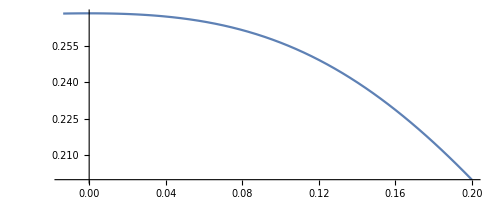

```mathematica
b=ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,1}]
```

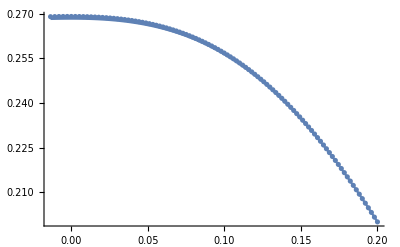

```mathematica
Show[a,b]
```

```mathematica
y[1]/.s
```

{1.33262}